# ApplyGraphEmbeddings

Visualize a graph by applying different graph embeddings

## Definition

```mathematica
ClearAll[ApplyGraphEmbeddings]
ApplyGraphEmbeddings[graph_?GraphQ]:=Select[GraphQ[#]&][AssociationMap[embedding↦Graph[graph,VertexCoordinates->GraphEmbedding[graph,embedding,2]],{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}]]
ApplyGraphEmbeddings[graph_?GraphQ,2]:=Select[GraphQ[#]&][AssociationMap[embedding↦Graph[graph,VertexCoordinates->GraphEmbedding[graph,embedding,2]],{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}]]
ApplyGraphEmbeddings[graph_?GraphQ,3]:=Select[GraphQ[#]&][AssociationMap[embedding↦Graph3D[graph,VertexCoordinates->GraphEmbedding[graph,embedding,3]],{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}]]
```

```mathematica
ApplyGraphEmbeddings[graph_?GraphQ]:=Select[GraphQ[#]&][AssociationMap[embedding↦Graph[graph,VertexCoordinates->GraphEmbedding[graph,embedding,2]],{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}]]
```

```mathematica
ApplyGraphEmbeddings[graph_?GraphQ,2]:=Select[GraphQ[#]&][AssociationMap[embedding↦Graph[graph,VertexCoordinates->GraphEmbedding[graph,embedding,2]],{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}]]
```

```mathematica
ApplyGraphEmbeddings[graph_?GraphQ,3]:=Select[GraphQ[#]&][AssociationMap[embedding↦Graph3D[graph,VertexCoordinates->GraphEmbedding[graph,embedding,3]],{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}]]
```

```mathematica
Apply3DGraphEmbeddings[graph_?GraphQ,3]:=Select[AssociationMap[embedding↦Graph3D[graph,VertexCoordinates->GraphEmbedding[graph,embedding,3]],{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}],GraphQ[#]&]
```

```mathematica
ApplyGraphEmbeddings[graph_?GraphQ,3]:=AssociationMap[embedding↦Graph,{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}]/;MatchQ[dimension,2|3]
```

## Documentation

### Usage

ApplyGraphEmbeddings[graph]

visualize graph by applying different graph embeddings

It might be better to just combine this with your other submission Apply3DGraphEmbeddings; just add a second argument to indicate if 2D or 3D embeddings are wanted.

ApplyGraphEmbeddings[graph,dimension]

visualize graph by applying different graph embeddings in dimension

### Details & Options

The graph embeddings might be identical.

The graph embedding dimension is 2 for plane embeddings by default. This can be changed with the second parameter to find 3D embeddings.

The dimension should be 2 or 3 for the plane and three dimensional space, respectively. The function will not evaluate if the dimension is not 2 or 3.

The function does not keep graph embeddings that do not work for a graph by using Select and GraphQ.

## Examples

### Basic Examples

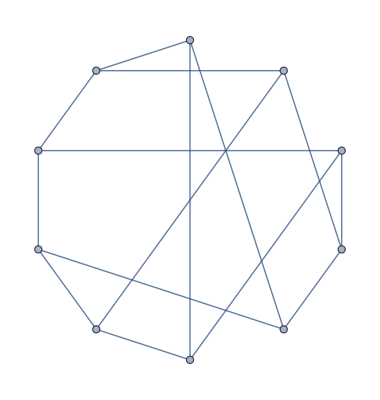
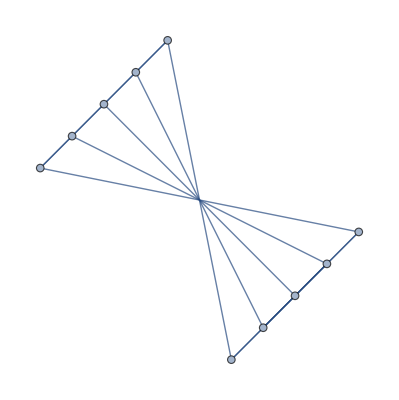
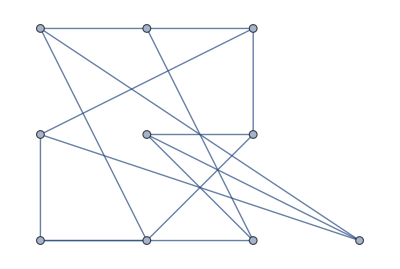
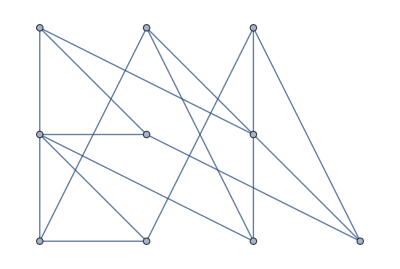
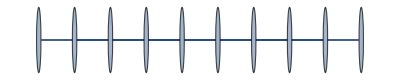
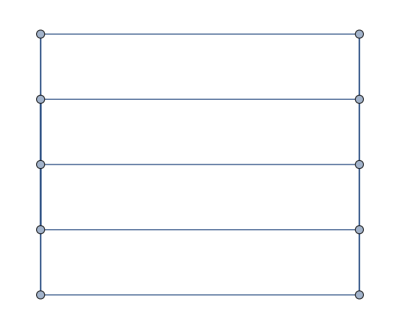
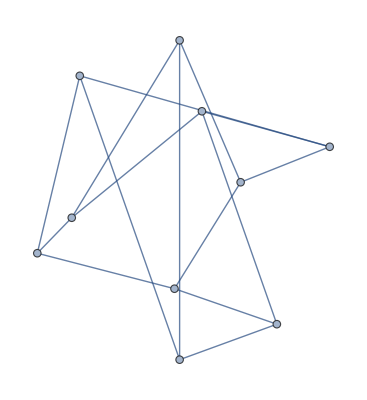
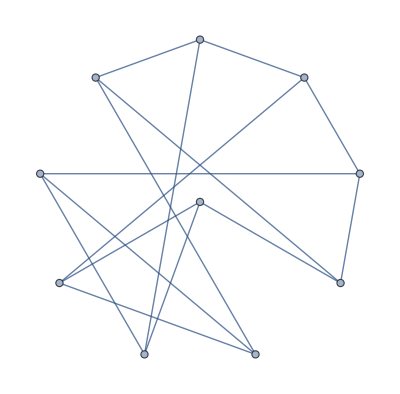
<|CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,SpiralEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-|>

```mathematica
ApplyGraphEmbeddings[PetersenGraph[]]
```

See different embeddings for a bipartite graph:

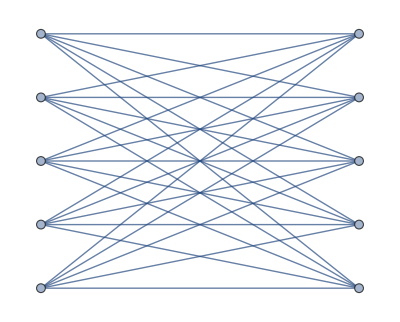
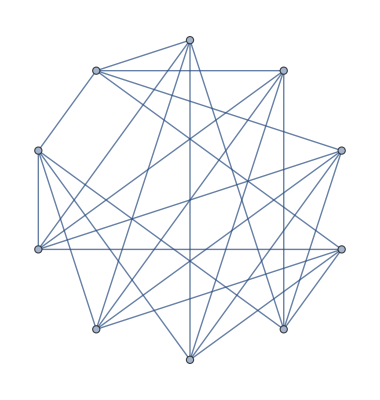
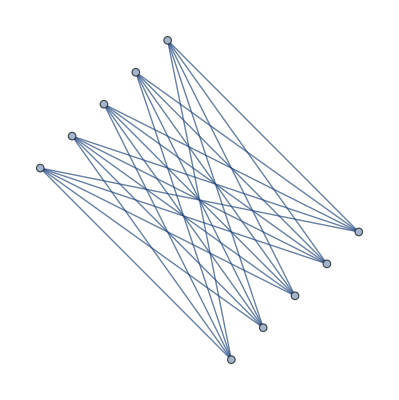
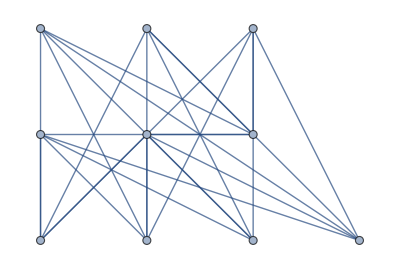
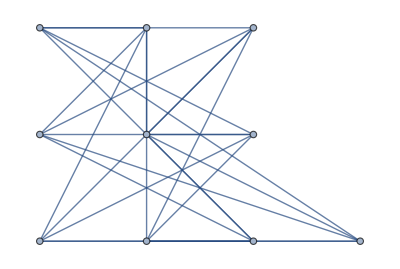
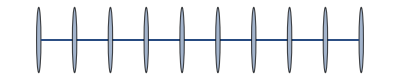
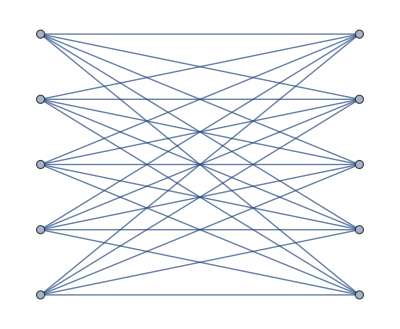
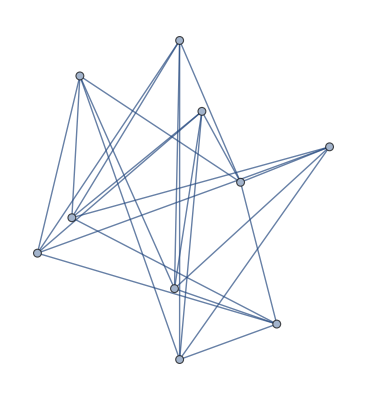
<|BipartiteEmbedding→-Graphics-,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,SpiralEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-|>

```mathematica
ApplyGraphEmbeddings[CompleteGraph[{5,5}]]
```

```mathematica
ApplyGraphEmbeddings[CompleteGraph[{5,5}],2]//AbsoluteTiming
```

{2.33058,<|BipartiteEmbedding→-Graphics-,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,SpiralEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-|>}

Visualize a buckyball graph in three dimensions:

```mathematica
ApplyGraphEmbeddings[BuckyballGraph[3],3]
```

<|CircularEmbedding→-Graphics3D-,CircularMultipartiteEmbedding→-Graphics3D-,DiscreteSpiralEmbedding→-Graphics3D-,GridEmbedding→-Graphics3D-,LinearEmbedding→-Graphics3D-,MultipartiteEmbedding→-Graphics3D-,SpiralEmbedding→-Graphics3D-,StarEmbedding→-Graphics3D-,BalloonEmbedding→-Graphics3D-,RadialEmbedding→-Graphics3D-,LayeredEmbedding→-Graphics3D-,GravityEmbedding→-Graphics3D-,HighDimensionalEmbedding→-Graphics3D-,PlanarEmbedding→-Graphics3D-,SpectralEmbedding→-Graphics3D-,SphericalEmbedding→-Graphics3D-,SpringElectricalEmbedding→-Graphics3D-,SpringEmbedding→-Graphics3D-,TutteEmbedding→-Graphics3D-|>

### Applications

### Properties and Relations

Apply graph embeddings to an alternating tree graph using the Resource Function Alternating Tree Graph:

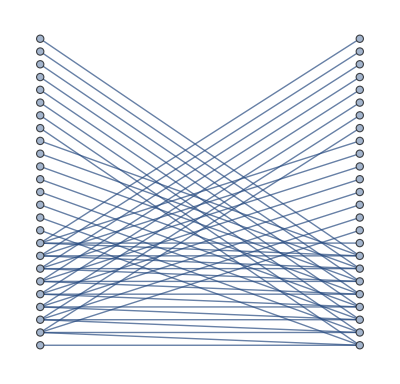
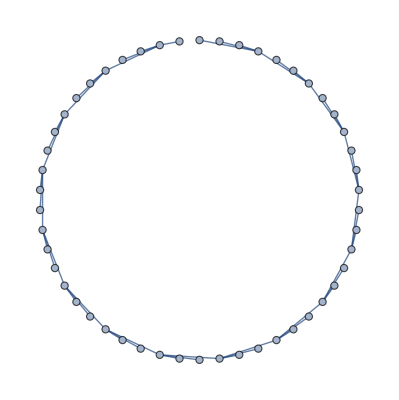
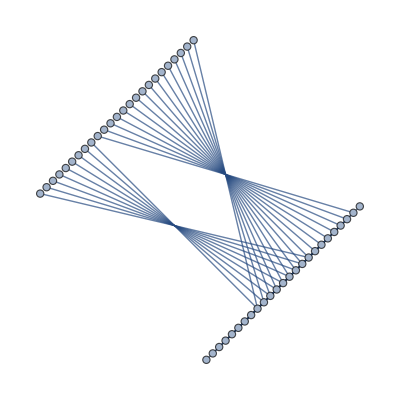
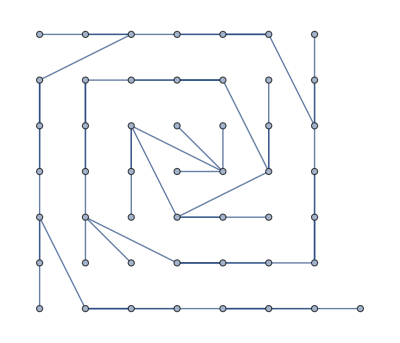
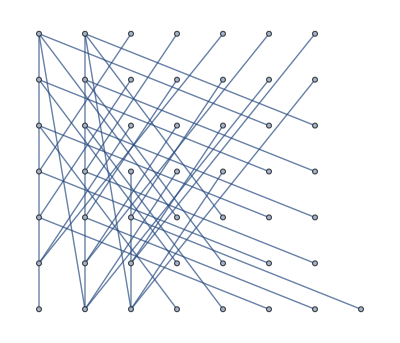
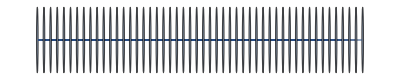
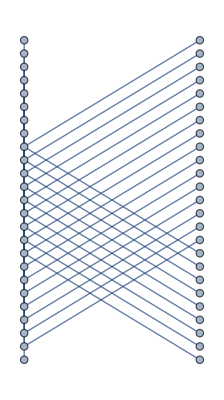
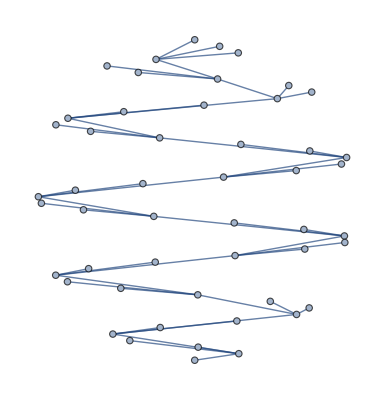
<|BipartiteEmbedding→-Graphics-,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,SpiralEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,PlanarEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-,TutteEmbedding→-Graphics-|>

```mathematica
ApplyGraphEmbeddings[ResourceFunction["AlternatingTreeGraph"][18]]
```

### Possible Issues

The dimension should be 2 or 3.

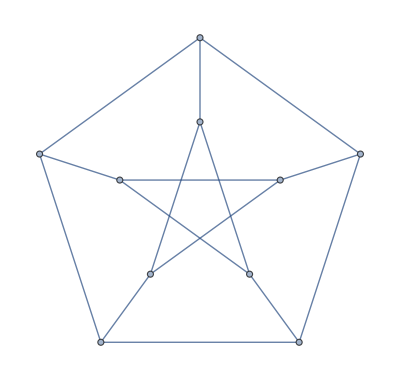
ApplyGraphEmbeddings[-Graphics-,4]

```mathematica
ApplyGraphEmbeddings[PetersenGraph[],4]
```

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Graph Embeddings

Topological graph theory

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

GraphEmbedding

VertexCoordinates

GraphLayout

Graph3D

GraphPlot

### Related Resource Objects

AlternatingTreeGraph

TriangularGridGraph

HexagonalGridGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

I am working on a function for 3D graph embeddings.